### Data Import - new analysis

#### Raw Data

```mathematica
mainDir=NotebookDirectory[]
```

C:\Users\KyleKeane\Dropbox (MIT)\Wolfram\Summer_Programs\Collaborations\hannah_kyle_shared_wss\

```mathematica
sampleDir=FileNameJoin[{mainDir,"Clean"}]
```

C:\Users\KyleKeane\Dropbox (MIT)\Wolfram\Summer_Programs\Collaborations\hannah_kyle_shared_wss\Clean

```mathematica
samples=FileNames[___,sampleDir];
```

```mathematica
legaldic=;
```

```mathematica
legalese=DeleteDuplicates@DeleteStopwords@StringSplit[legaldic];
```

```mathematica
caseNumbersFromTranscripts=Map[FileBaseName,samples];
```

```mathematica
datafolder=FileNameJoin[{mainDir,"Data"}]
```

C:\Users\KyleKeane\Dropbox (MIT)\Wolfram\Summer_Programs\Collaborations\hannah_kyle_shared_wss\Data

```mathematica
numericData=First@Import[FileNameJoin[{datafolder,"SCDB_2017_01_justiceCentered_Docket_numbers.xlsx"}]];
```

```mathematica
keepThese=Flatten@Position[numericData[[1]],"docket"|"caseDisposition"|"justiceName"|"vote",{1}];
```

```mathematica
goodColumns=Part[numericData,All,keepThese];
```

```mathematica
Dimensions@goodColumns
```

{91764,4}

```mathematica
matchingCases=Select[goodColumns,MemberQ[caseNumbersFromTranscripts,#[[1]]]&];
```

```mathematica
Dimensions@matchingCases
```

{31723,4}

```mathematica
goodDockets=Select[matchingCases,StringContainsQ[#[[1]],"-"]&];
```

```mathematica
goodDockets//Dimensions
```

{31723,4}

```mathematica
votesAndOutcomes=Part[GroupBy[goodDockets,First],All,All,{3,4,2}];
```

#### sortedFullData

```mathematica
fullData=KeyValueMap[<|
"Docket"->#1,
"Decisions"->#2,
"RawText"->Import@First@Select[samples,Function[{file},StringContainsQ[file,#1]]]|>&,votesAndOutcomes];
```

```mathematica
sortedFullData=SortBy[fullData,ToExpression@First@StringSplit[#["Docket"],"-"]&];
```

#### finalData with parsed conversations

```mathematica
good=Map[
Function[
{case},
hasAppearancesQ=StringContainsQ[
case["RawText"],
"APPEARANCES"
];
hasProceedingsQ=StringContainsQ[
case["RawText"],
Alternatives["PROCEEDINGS","P R O C E E D I N G S"]
];
Which[
Not@hasAppearancesQ&&Not@hasProceedingsQ,
Nothing,
True,
Append[case,"Conversations"->Last@StringSplit[case["RawText"],Alternatives["PROCEEDINGS","P R O C E E D I N G S","APPEARANCES"]]]
]
],
sortedFullData
];
```

```mathematica
good2=MapAt[
StringSplit[
#,
n:Join[CharacterRange["A","Z"],{" ","."}]..~~":":>n
]&,
good,
{All,"Conversations"}
];
```

```mathematica
finalData=MapAt[
SequenceCases[
StringTrim/@#,{name_/;StringMatchQ[name,Join[CharacterRange["A","Z"],{" ","."}]..],_}
]&,
good2,
{All,"Conversations"}
];
```

```mathematica
sortedFullData//Dimensions
```

{3514}

#### export data for later

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"finalData.wxf"}],finalData,"WXF"];
```

#### cloud put

```mathematica
(*CloudPut[finalData,"junk/data",Permissions->"Public"]*)
```

### Using cached data

#### button

```mathematica
Button[
"Run from here down",
Function[
{cell},
SelectionMove[cell,All,Cell,AutoScroll->False];
FrontEndTokenExecute[EvaluationNotebook[],"EvaluateCells"]
]/@Part[
Cells@EvaluationNotebook[],Position[Cells@EvaluationNotebook[],EvaluationCell[]][[1,1]]+1;;-1
],
Method->"Queued"
]
```

Run from here down

#### Importing local cached data

```mathematica
finalData=Import[FileNameJoin[{NotebookDirectory[],"finalData.wxf"}]];
```

#### CloudGet

```mathematica
(*CloudPut[finalData,"junk/data",Permissions->"Public"]*)
```

### educational example of looking at a particular justice

#### do it on one to develop code

```mathematica
justice="WHRehnquist";
lastName="REHNQUIST";
```

```mathematica
finalData[[1,"Docket"]]
```

00-1011

```mathematica
(*this might be Missing[]*)
decisions=FirstCase[finalData[[1,"Decisions"]],{justice,theirVote_,fullVote_}:>{theirVote,fullVote}]
```

{2.,2.}

```mathematica
Cases[finalData[[1,"Conversations"]],{name_/;StringContainsQ[name,lastName],said_}:>said]
```

{We'll hear argument
now in Number 00-1011, Deboris Calcano-Martinez v. The
Immigration and Naturalization Service.
Mr. Guttentag.
ORAL ARGUMENT OF LUCAS GUTTENTAG
ON BEHALF OF THE PETITIONER,Thank you,
Mr. Guttentag.  The case is submitted.
(Whereupon, at 11:17 a.m., the case in the
above-entitled matter was submitted.)}

#### development

```mathematica
getDocket[case_]:=case[["Docket"]]
```

```mathematica
(*this might be Missing[]*)
getDecisions[case_,justice_]:=FirstCase[case[["Decisions"]],{justice,theirVote_,fullVote_}:>{theirVote,fullVote}]
```

```mathematica
getOutcome[case_]:=case[["Decisions",1,3]]
```

```mathematica
getConversations[case_,lastName_]:=Cases[case[["Conversations"]],{name_/;StringContainsQ[name,lastName],said_}:>said]
```

#### eachvote

```mathematica
justiceLastName={{"NMGorsuch","GORSUCH"},{"EKagan","KAGAN"},{"SSotomayor","SOTOMAYOR"},{"SAAlito","ALITO"},{"JGRoberts","ROBERTS"},{"SGBreyer","BREYER"},{"RBGinsburg","GINSBURG"},{"CThomas","THOMAS"},{"DHSouter","SOUTER"},{"AMKennedy","KENNEDY"},{"AScalia","SCALIA"},{"SDOConnor","CONNOR"},{"JPStevens","STEVENS"},{"WHRehnquist","REHNQUIST"},{"LFPowell","POWELL"},{"HABlackmun","BLACKMUN"},{"WEBurger","BURGER"},{"TMarshall","MARSHALL"},{"BRWhite","WHITE"},{"PStewart","STEWART"},{"WJBrennan","BRENNAN"}};
```

```mathematica
finalVote[{justice_,lastName_}]:=Module[
{timelineVote,voteto,associate},
timelineVote={getDecisions[#,justice],getConversations[#,lastName]}&/@finalData;
voteto=DeleteMissing[Union[timelineVote],2]/.{}->{""};
associate=#2->#1&@@@Select[voteto,Length[#]==2&];
associate
]
```

```mathematica
eachvote=AssociationMap[finalVote,justiceLastName];
```

```mathematica
mergedVotes=MapAt[
Replace[
Replace[
#,
{
{1.,n_}:>{1,n},
{2.,n_}:>{2,n},
{3.|4.,n_}:>{3,n},
{5.|6.|7.|"",n_}:>{4,n},
{8.,n_}:>{5,n}
},
{0}
],
{
{n_,2.}:>ToString@{n,2},
{n_,3.}:>ToString@{n,3},
{n_,4.}:>ToString@{n,4},
{n_,5.|6.|7.}:>ToString@{n,5},
{n_,8.|9.|10.}:>ToString@{n,6}
}
]&,
eachvote,
{All,All,2}
];
```

```mathematica
significantConvo=Keys@Select[Map[Length,mergedVotes],#>300&]
```

{{EKagan,KAGAN},{SSotomayor,SOTOMAYOR},{SAAlito,ALITO},{JGRoberts,ROBERTS},{SGBreyer,BREYER},{RBGinsburg,GINSBURG},{DHSouter,SOUTER},{AMKennedy,KENNEDY},{AScalia,SCALIA},{JPStevens,STEVENS},{WHRehnquist,REHNQUIST},{WEBurger,BURGER}}

### bag of words classifier

#### worked example

drop uncommon words

```mathematica
readyForClassify=MapAt[ToString,MapAt[StringJoin,mergedVotes[{"WHRehnquist","REHNQUIST"}],{All,1}],{All,2}];
```

```mathematica
{trainingData,testingData}=TakeDrop[RandomSample@readyForClassify,IntegerPart[0.8 Length[readyForClassify]]];
```

```mathematica
Length@trainingData
```

1312

```mathematica
fakeJudge=Classify[trainingData]
```

ClassifierFunction[…]

```mathematica
judgeOfFakeJudge=ClassifierMeasurements[fakeJudge,testingData]
```

ClassifierMeasurementsObject[…]

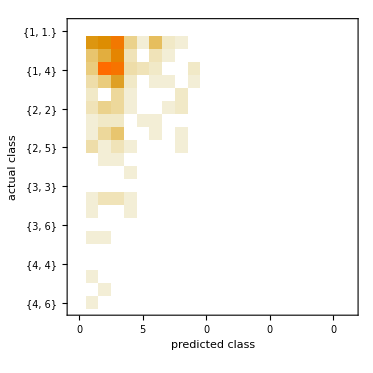

```mathematica
judgeOfFakeJudge["ConfusionMatrixPlot"]
```

### Machine Learning for Each Justice - Pure Text

#### wordBag

```mathematica
wordbag[votes_,{justice_,lastName_}]:=Module[
{readyForClassify,trainingData,testingData,fakeJudge,judgeOfFakeJudge},
readyForClassify=MapAt[ToString,MapAt[StringJoin,votes[{justice,lastName}],{All,1}],{All,2}];
{trainingData,testingData}=TakeDrop[RandomSample@readyForClassify,IntegerPart[0.8 Length[readyForClassify]]];
Length[trainingData];
fakeJudge=Classify[trainingData];
 ClassifierMeasurements[fakeJudge,testingData]
]
```

#### Accuracy of each

```mathematica
classifierMeasurements=AssociationMap[wordbag[mergedVotes,#]&,significantConvo];
```

```mathematica
Counts@RandomChoice[Range@25,1000]/1000//N
```

<|10→0.038,23→0.045,3→0.045,12→0.043,19→0.044,2→0.036,11→0.045,7→0.045,17→0.048,15→0.034,14→0.044,1→0.043,8→0.047,24→0.043,6→0.037,13→0.03,20→0.042,18→0.042,5→0.025,4→0.039,16→0.035,22→0.04,21→0.046,25→0.034,9→0.03|>

#### Machine Learning Plot

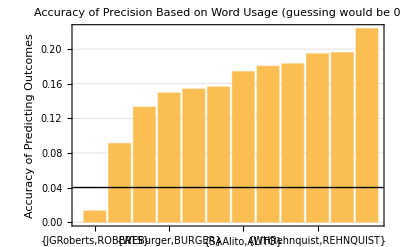

```mathematica
BarChart[Sort@KeyValueMap[Labeled[#2,Rotate[#1,Pi/2]]&,Map[#["Accuracy"]&,classifierMeasurements]],Frame->True,PlotTheme->"Detailed",FrameLabel->"Accuracy of Predicting Outcomes",PlotLabel->"Accuracy of Precision Based on Word Usage\n(guessing would be 0.04)",Epilog->Line[{{0,.04},{10000,.04}}]]
```

### sentiment analysis

#### sentiment

```mathematica
MapAt[Chop@Classify["Sentiment",#,"Probability"->"Negative"]&,mergedVotes[[1]][[2]],{1,All}]
```

{0.201241,1.,0.403824,0.999919,0.201241,0.000247628,0.0991976}→{1, 2}

```mathematica
(*sentiment takes a long time to run*)
sentimentToVote=Map[Function[{vote},MapAt[Chop@Classify["Sentiment",#,"Probability"->"Negative"]&,vote,{1,All}]],KeyTake[mergedVotes,significantConvo],{2}];
```

```mathematica
Length[sentimentToVote]
```

12

```mathematica
Select[sentimentToVote,Length[#]≥300&]//Length
```

12

```mathematica
sentimentToVote[[1]];
```

#### Sentiment Histograms

```mathematica
Rasterize@Dataset[Histogram[Flatten@#[[All,1]],10]&/@sentimentToVote]
```

-Graphics-

```mathematica
Classify["Sentiment",eachvote[[1]][[2]][[1,4]],"Probabilities"]
```

<|Positive→6.32569×10^-15,Neutral→0.000080767,Negative→0.999919|>

## Data Visualization

### Word Frequency

#### Recoding Data

```mathematica
sampleDirw=FileNameJoin[{NotebookDirectory[],"Clean"}];
```

```mathematica
samplew=FileNames[___,sampleDirw];
```

```mathematica
numericDataw=First@Import[FileNameJoin[{datafolder,"SCDB_2017_01_justiceCentered_Docket_numbers.xlsx"}]];
```

```mathematica
keepThesew=Flatten@Position[numericDataw[[1]],"docket"|"caseDisposition"|"justiceName"|"vote",{1}];
```

```mathematica
goodColumnsw=Part[numericDataw,All,keepThesew];
```

```mathematica
caseNumbersFromTranscriptsw=Map[FileBaseName,samplew];
```

{00-1011,00-1021,00-1045,00-10666,00-1072,00-1073,00-1089,00-1167,00-1187,00-1214,00-121,00-1249,00-1250,00-1260,00-1293,00-1307,00-1406,00-1471,00-1514,00-1519,00-151,00-152,00-1531,00-1543,00-1567,00-157,00-1595,00-1614,00-1737,00-1751,00-1770,00-1831,00-1853,00-189,00-191,00-1937,00-201,00-203,00-24,00-276,00-292,00-346,00-347,00-391,00-454,00-492,00-507,00-511,00-5250,00-549,00-568,00-5961,00-596,00-6029,00-6374,00-6567,00-6677,00-6933,00-730,00-758,00-763,00-767,00-795,00-799,00-832,00-836,00-8452,00-853,00-860,00-878,00-927,00-9280,00-9285,00-949,00-952,00-957,00-973,01-1015,01-1067,01-10873,01-1107,01-1118,01-1120,01-1127,01-1184,01-1209,01-1229,01-1231,01-1243,01-1269,01-1289,01-131,01-1325,01-1368,01-1375,01-1418,01-1420,01-1435,01-1437,01-1444,01-147,01-1491,01-1500,01-1559,01-1572,01-1757,01-1806,01-1862,01-188,01-270,01-298,01-301,01-309,01-332,01-344,01-394,01-400,01-408,01-417,01-419,01-455,01-463,01-46,01-488,01-518,01-521,01-584,01-593,01-595,01-618,01-631,01-651,01-653,01-679,01-682,01-687,01-6978,01-704,01-705,01-706,01-714,01-729,01-7574,01-757,01-7662,01-800,01-896,01-9094,01-950,01-963,02-10038,02-1016,02-102,02-1060,02-1080,02-1183,02-1196,02-1205,02-1238,02-1290,02-1315,02-1343,02-1348,02-1371,02-1377,02-1389,02-1472,02-1541,02-1580,02-1593,02-1603,02-1606,02-1609,02-1624,02-1632,02-1657,02-1667,02-1672,02-1674,02-1684,02-1689,02-1794,02-1809,02-1824,02-182,02-1845,02-196,02-215,02-241,02-258,02-271,02-281,02-299,02-306,02-311,02-337,02-361,02-371,02-403,02-428,02-42,02-458,02-469,02-473,02-516,02-524,02-5664,02-572,02-575,02-626,02-628,02-6320,02-634,02-658,02-6683,02-679,02-682,02-693,02-695,02-69,02-722,02-749,02-763,02-809,02-811,02-819,02-8286,02-857,02-891,02-9065,02-9410,02-94,02-954,02-964,03-10198,03-101,03-1027,03-1039,03-107,03-1116,03-1160,03-1164,03-1230,03-1237,03-1238,03-1293,03-1388,03-1395,03-13,03-1407,03-1423,03-1454,03-1488,03-1500,03-1566,03-1601,03-167,03-1693,03-1696,03-184,03-218,03-221,03-287,03-334,03-339,03-358,03-388,03-407,03-409,03-44,03-475,03-5165,03-526,03-5554,03-633,03-636,03-6539,03-6696,03-6821,03-710,03-724,03-725,03-750,03-814,03-855,03-8661,03-878,03-892,03-9046,03-9168,03-923,03-931,03-932,03-9560,03-95,03-9627,03-9659,03-9685,03-9877,04-1034,04-104,04-10566,04-1067,04-1084,04-108,04-1131,04-1140,04-1144,04-1152,04-1170b,04-1170,04-1186,04-1203,04-1244,04-1264,04-1324,04-1327,04-1329,04-1332,04-1350,04-1360,04-1371,04-1376,04-1414,04-1477,04-1495,04-1506,04-1527,04-1528,04-1544,04-1581,04-1618,04-163,04-169,04-1704,04-1739,04-277,04-278,04-340,04-368,04-373,04-37,04-433,04-473b,04-473,04-480,04-495,04-514,04-5286,04-5293,04-52,04-5462,04-563,04-5928,04-593,04-597,04-603,04-607,04-623,04-631,04-637,04-6432,04-6964,04-698,04-70,04-712,04-721,04-759,04-805,04-848,04-881,04-885,04-8990,04-905,04-928,04-944,04-9728,04-980,05-1056,05-1074,05-1120,05-1126,05-11284,05-11304,05-1157,05-1240,05-1256,05-1272,05-1284,05-128,05-130,05-1342,05-1345,05-1382,05-1429,05-1448,05-1508,05-1541,05-1575,05-1589,05-1629,05-1631,05-184,05-18,05-200,05-204,05-259,05-260,05-352,05-380,05-381,05-409,05-416,05-465,05-493,05-502,05-5224,05-547,05-5705,05-593,05-595,05-5966,05-5992,05-608,05-6551,05-669,05-7053,05-7058,05-705,05-746,05-785,05-83,05-848,05-85,05-8794,05-8820,05-908,05-915,05-9222,05-9264,05-983,05-996,05-998,06-1005,06-10119,06-102,06-1037,06-1082,06-11206,06-11429,06-11543,06-11612,06-1164,06-116,06-1181,06-1195,06-1204,06-1221,06-1249,06-1265,06-1286,06-1287,06-1321,06-1322,06-134or,06-134,06-1413,06-1431,06-1456,06-1457,06-1463,06-1498,06-1505,06-1509,06-157,06-1595,06-1646,06-1666,06-1717,06-179,06-219,06-278,06-313,06-340,06-376,06-413,06-427,06-43,06-457,06-480,06-484,06-5247,06-5306,06-531,06-5618,06-562,06-571,06-5754,06-593,06-618,06-6330,06-637,06-6407,06-666,06-6911,06-694,06-713,06-7517,06-766,06-7949,06-8120,06-8273,06-84,06-856,06-9130,06-923,06-937,06-939,06-969,06-984,06-989,07-1015,07-10374,07-10441,07-1059,07-1090,07-1114,07-11191,07-1122,07-1125,07-1209,07-1216,07-1223,07-1239,07-1309,07-1315,07-1356,07-1372,07-1410,07-1428,07-1437,07-1529,07-1601,07-208,07-210,07-214,07-219,07-21,07-290,07-308,07-312,07-320,07-330,07-343,07-371,07-411,07-440,07-455,07-463,07-474,07-499,07-512,07-513,07-526,07-542,07-5439,07-543,07-544,07-552,07-562,07-581,07-582,07-588,07-591,07-6053,07-608,07-610,07-615,07-636,07-665,07-689,07-6984,07-751,07-772,07-773,07-77,07-8521,07-854,07-869,07-901,07-9712,07-984,07-9995,08-1008,08-103,08-1065,08-108,08-1107,08-1119,08-1134,08-1151,08-1175,08-1191,08-1196,08-1198,08-1200,08-1214,08-1224,08-1301,08-1314,08-1322,08-1332,08-1341,08-1371,08-1394,08-1402,08-1423,08-1438,08-1448,08-1457,08-146,08-1470,08-1498,08-1521,08-1529,08-1553,08-1555,08-1569,08-192,08-205[R,08-205,08-214,08-22,08-240,08-267,08-289,08-295,08-304,08-305,08-310,08-322,08-351,08-441,08-453,08-472,08-479,08-495,08-5274,08-538,08-586,08-598,08-604,08-6261,08-645,08-651,08-660,08-661,08-674,08-678,08-67,08-680,08-681,08-6925,08-6,08-724,08-728,08-7412,08-7621,08-769,08-810,08-861,08-876,08-88,08-905,08-911,08-9156,08-964,08-969,08-970,08-974,08-992,08-998,09-10245,09-1036,09-10876,09-1088,09-11121,09-11311,09-11328,09-11556,09-1156,09-1159,09-115,09-1163,09-1205,09-1227,09-1233,09-1272,09-1273,09-1279,09-1298,09-1343,09-1403,09-1454,09-1476,09-1498,09-150,09-152,09-1533,09-158,09-223,09-291,09-329,09-337,09-338,09-350,09-367,09-400,09-448,09-475,09-479,09-497,09-5201,09-520,09-525,09-529,09-530,09-5327,09-559,09-571,09-5801,09-587,09-60,09-6338,09-658,09-6822,09-737,09-751,09-804,09-834,09-837,09-846,09-868,09-893,09-9000,09-907,09-958,09-987,09-993,09-996,10-1001,10-1016,10-1018,10-1024,10-1042,10-1062,10-10,10-1104,10-1121,10-114,10-1150,10-1195,10-1211,10-1219,10-1259,10-1261,10-1265,10-1293,10-1320,10-1399,10-1472,10-1491r,10-1491,10-1542,10-174,10-179,10-188,10-209,10-218,10-224,10-235,10-238,10-277,10-290,10-313,10-382,10-444,10-507,10-5258,10-5400,10-5443,10-545,10-553,10-568,10-577,10-637,10-63,10-6549,10-680,10-694,10-699,10-6,10-704,10-708,10-7387,10-76,10-779,10-788,10-8145,10-844,10-8505,10-875,10-879,10-895,10-8974,10-930,10-945,10-948,10-9646,10-9647,10-98,10-9995,11-10189,11-1025,11-10362,11-1059,11-1085,11-1118-,11-1160,11-1175,11-1221,11-1231,11-1274,11-1285,11-1327,11-1347,11-1351,11-139,11-1425,11-1447,11-1450,11-1518,11-1545,11-159,11-161,11-166,11-182,11-184,11-192,11-199,11-204,11-210,11-218,11-246,11-262,11-338,11-345,11-393,11-398,11-400,11-45,11-460,11-465,11-551,11-556,11-564,11-5683,11-597,11-626,11-681,11-697,11-702,11-713,11-770,11-796,11-798,11-817,11-820,11-864,11-889,11-88,11-8976,11-9307,11-9335,11-94,11-9540,11-965,11-982,11-9953,12-1036,12-1038,12-10882,12-10,12-1117,12-1128,12-1146,12-1163,12-1168,12-1173,12-1182,12-1184,12-1200,12-1226,12-123,12-126,12-1281,12-1315,12-133,12-135,12-1371,12-138,12-1408,12-142,12-144,12-1493,12-1497,12-158,12-167,12-17,12-207,12-236,12-246,12-25,12-307,12-315,12-357,12-398,12-399,12-3,12-414,12-416,12-417,12-418,12-43,12-462,12-464,12-484,12-515,12-5196,12-52,12-536,12-547,12-562,12-574,12-609,12-62,12-682,12-696,12-71,12-729,12-7515,12-751,12-761,12-7822,12-786,12-794,12-79,12-815,12-820,12-842,12-8561,12-872,12-873,12-895,12-9012,12-929,12-930,12-9490,12-96,12-98,12-992,12-99,13-1010,13-1019,13-1032,13-1034,13-1041,13-1074,13-1075,13-1080,13-115,13-1174,13-1175,13-1211,13-1314,13-132,13-1333,13-1352,13-1371,13-1402,13-1412,13-1421,13-1428,13-1433,13-1487,13-1499,13-193,13-212,13-271,13-298,13-299,13-301,13-316,13-317,13-339,13-352,13-354,13-369,13-433,13-435,13-461,13-483,13-485,13-502,13-517,13-534,13-550,13-553,13-604,13-628,13-6827,13-684,13-7120,13-719,13-720,13-7211,13-7451,13-854,13-894,13-895,13-896,13-9026,13-935,13-975,13-983,13-9972,14-103,14-1055,14-114,14-116,14-144,14-1538,14-15,14-185,14-275,14-378,14-400,14-46,14-556,14-6368,14-7955,14-86,14-9496,15-1031,15-1039,15-1111,15-1189,15-118,15-1191,15-1194,15-1204,15-1248,15-1251,15-1256,15-1262,15-1293,15-1358,15-1391,15-1406,15-1439,15-1485,15-1498,15-1500,15-1503,15-1509,15-214,15-423,15-457,15-497,15-513,15-537,15-577,15-5991,15-606,15-628,15-649,15-680,15-7250,15-777,15-797,15-8049,15-827,15-8544,15-866,15-9260,15-927,16-1011,16-1027,16-1067,16-111,16-1140,16-1144,16-1150,16-1161,16-1215,16-1220,16-1276,16-1348,16-1362,16-1371,16-142,16-1432,16-1435,16-1454,16-1466,16-1495,16-149,16-1519,16-240,16-254,16-285,16-299,16-309,16-327,16-32,16-341,16-348,16-349,16-369,16-373,16-399,16-402,16-405,16-424,16-460,16-466,16-476,16-498,16-499,16-5294,16-529,16-534,16-54,16-605,16-6219,16-658,16-6795,16-6855,16-712,16-74,16-784,16-8255,16-9493,16-961,16-969,16-980,17-130,17-155,17-21,17-269,17-2,17-312,17-333,17-387,17-432,17-43,17-459,17-494,17-530,17-5639,17-5716,17-586,17-965,78-1545,78-1789,78-1841,78-1945,79-1003,79-1013,79-1033,79-1056,79-1068,79-1112,79-1127,79-1128,79-1144,79-1157,79-1171,79-1176,79-1186,79-1213,79-1236,79-1252,79-1260,79-1266,79-1320,79-1336,79-1344,79-1380,79-1388,79-1404,79-1420,79-1423,79-1429,79-1515,79-1517,79-1538,79-1601,79-1618,79-1631,79-1640,79-1709,79-1711,79-1734,79-1738,79-1740,79-1764,79-1777,79-1794,79-1890,79-1907,79-1943,79-1944,79-1952,79-1977,79-1997,79-2006,79-395,79-404,79-408,79-512,79-5269,79-5602,79-567,79-5688,79-5780,79-5903,79-5932,79-5949,79-5962,79-6027,79-621,79-6423,79-6624,79-6740,79-6777,79-6779,79-6853,79-700,79-770,79-814,79-816,79-824,79-855,79-870,79-880,79-886,79-900,79-927,79-935,79-938,79-939,79-952,79-983,80-1002,80-1012,80-1045,80-1070,80-1074,80-1082,80-1121,80-1146,80-1188,80-1190,80-1199,80-11,80-1208,80-120,80-1240,80-1251,80-1285,80-1290,80-1305,80-1345,80-1348,80-1349,80-1350,80-1377,80-1417,80-1429,80-1430,80-1431,80-1436,80-1437,80-1464,80-1481,80-148,80-1496,80-1538,80-1556,80-1562,80-1576,80-1577,80-1582,80-1594,80-1595,80-1608,80-1614,80-1663,80-1666,80-1681,80-1690,80-169,80-1714,80-1730,80-1735,80-1745,80-1749,80-1765,80-1798,80-180,80-1832,80-1874,80-1924,80-1925,80-1952,80-195,80-1990,80-2015,80-202,80-203,80-2043,80-2049,80-2070,80-2078,80-207,80-2100,80-2102,80-2116,80-2134,80-2146,80-2147,80-2150,80-2162,80-2165,80-2177,80-2178,80-2182,80-2195,80-2204,80-2205,80-2209,80-231,80-242,80-251,80-264,80-289,80-298,80-317,80-327,80-328,80-332,80-348,80-396,80-415,80-419,80-420,80-427,80-429,80-441,80-5049,80-5060,80-518,80-5303,80-5392,80-544,80-5727,80-581,80-5887,80-5889,80-590,80-5950,80-5,80-6045,80-608,80-60,80-6298,80-644,80-6680,80-689,80-702,80-710,80-737,80-756,80-757,80-767,80-780,80-795,80-802,80-808,80-824,80-83,80-846,80-847,80-848,80-84,80-850,80-885,80-901,80-931,80-939,80-965,80-986,80-988,80-990,81-1003,81-1008,81-1020,81-1032,81-1044,81-1062,81-1064,81-1095,81-1114,81-1120,81-1180,81-1181,81-1196,81-1203,81-1214,81-1222,81-1244,81-1251,81-1255,81-1271,81-1273,81-129,81-1304,81-1314,81-1320,81-1335,81-1350,81-1370,81-1374,81-1404,81-1453,81-1463,81-1476,81-1487,81-1489,81-1493,81-1494,81-1506,81-150,81-1536,81-1574,81-1578,81-1581,81-1590,81-1613,81-1617,81-1627,81-1635,81-1661,81-1664,81-1675,81-1686,81-1687,81-1717,81-1748,81-1756,81-1794,81-1802,81-1839,81-1843,81-184,81-1857,81-1859,81-185,81-1863,81-1889,81-1891,81-1893,81-1938,81-1945,81-1966,81-1983,81-1985,81-1,81-202,81-2057,81-2101,81-2110,81-2125,81-212,81-213,81-2147,81-2149,81-2150,81-2159,81-2169,81-2245,81-2257,81-225,81-2318,81-2332,81-2337,81-2338,81-2386,81-2394,81-2399,81-244,81-280,81-298,81-300,81-31,81-328,81-334,81-341,81-349,81-389,81-38,81-395,81-406,81-411,81-419,81-420,81-430,81-431,81-440,81-450,81-451,81-460,81-469,81-485,81-497,81-5114,81-5152,81-5195,81-523,81-525,81-5321,81-534,81-535,81-554,81-55,81-574,81-611,81-613,81-614,81-61,81-622,81-638,81-6633,81-6756,81-680,81-6908,81-708,81-731,81-746,81-750,81-757,81-770,81-773,81-776,81-802,81-825,81-827,81-857,81-878,81-896,81-897,81-89,81-920,81-927,81-969,81-984,81-9,82-1005,82-1031,82-1041,82-1047,82-1050,82-1066,82-1071,82-1095,82-1127,82-1135,82-1150,82-1167,82-1186,82-118,82-11,82-1200,82-1213,82-1246,82-1248,82-1253,82-1256,82-1260,82-1271,82-1295,82-131,82-1326,82-1330,82-1349,82-1371,82-1401,82-1432,82-1448,82-1453,82-1474,82-1479,82-1554,82-1565,82-1577,82-1579,82-15,82-1608,82-1616,82-1630,82-1643,82-1651,82-167,82-1684,82-168,82-1721,82-1724,82-1734,82-1766,82-1771,82-1772,82-1795,82-1832,82-1845,82-185,82-1860,82-1889,82-1913,82-1922,82-195,82-1988,82-1994,82-1998,82-2042,82-2056,82-206,82-2113,82-2120,82-2140,82-2157,82-215,82-23,82-242,82-256,82-271,82-276,82-282,82-331,82-342,82-34,82-354,82-357,82-372,82-374,82-401,82-411,82-432,82-472,82-485,82-486,82-492,82-500,82-502,82-5119,82-524,82-5279,82-5298,82-52,82-5466,82-556,82-5576,82-585,82-5920,82-599,82-6080,82-618,82-629,82-63,82-65,82-660,82-6840,82-687,82-695,82-708,82-729,82-738,82-766,82-786,82-792,82-799,82-818,82-825,82-827,82-849,82-862,82-874,82-898,82-912,82-914,82-91,82-940,82-945,82-958,82-960,82-963,82-973,82-975,83-1007,83-1013,83-1015,83-1020,83-1032,83-1035,83-1065,83-1075,83-1097,83-1132,83-1153,83-1158,83-1170,83-1266,83-1274,83-128,83-1292,83-1307,83-1329,83-1330,83-1334,83-1360,83-1362,83-1368,83-1378,83-1394,83-1416,83-141,83-1427,83-1437,83-1452,83-1466,83-1476,83-1492,83-1545,83-1569,83-1590,83-1620,83-1622,83-1623,83-1624,83-1625,83-1632,83-1660,83-1673,83-1708,83-173,83-1748,83-1750,83-1785,83-1798,83-1807,83-1842,83-185,83-1878,83-1894,83-18,83-1911,83-1919,83-1925,83-1935,83-1944,83-1961,83-1968,83-196,83-1,83-2004,83-2030,83-2032,83-2064,83-2097,83-2126,83-2129,83-2136,83-2143,83-2146,83-2148,83-2161,83-2166,83-218,83-219,83-226,83-240,83-245,83-264,83-271,83-276,83-297,83-305,83-317,83-321,83-328,83-346,83-371,83-372,83-436,83-458,83-469,83-490,83-491,83-498,83-529,83-5424,83-558,83-5596,83-56,83-5954,83-6061,83-614,83-620,83-630,83-6607,83-6663,83-6766,83-703,83-710,83-712,83-724,83-727,83-728,83-747,83-751,83-773,83-812,83-832,83-838,83-850,83-859,83-87,83-904,83-912,83-916,83-935,83-95,83-963,83-96,83-990,83-997,84-1023,84-1044,84-1070,84-1076,84-1077,84-1097,84-1103,84-1144,84-1160,84-1181,84-1198,84-1236,84-1240,84-1244,84-1259,84-1273,84-1274,84-1279,84-127,84-1288,84-1321,84-1340,84-1360,84-1361,84-1362,84-1379,84-1479,84-1480,84-1484,84-1485,84-1491,84-1493,84-1503,84-1513,84-1529,84-1531,84-1538,84-1554,84-1555,84-1560,84-1580,84-1586,84-1601,84-1602,84-1606,84-1616,84-1636,84-1640,84-1644,84-1656,84-165,84-1661,84-1667,84-1686,84-16,84-1717,84-1725,84-1726,84-1728,84-1737,84-1744,84-1777,84-1803,84-1809,84-1839,84-1865,84-1903,84-1904,84-1905,84-1913,84-1922,84-1923,84-1944,84-1947,84-1948,84-194,84-1972,84-1973,84-1974,84-1979,84-1999,84-2015,84-2022,84-2030,84-231,84-233,84-237,84-249,84-261,84-262,84-277,84-28,84-310,84-312,84-320,84-325,84-335,84-351,84-363,84-433,84-435,84-438,84-465,84-468,84-476,84-489,84-48,84-495,84-497,84-498,84-4,84-5004,84-5059,84-5108,84-510,84-518,84-5240,84-5555,84-5630,84-571,84-5743,84-5786,84-5872,84-589,84-592,84-6075,84-6263,84-6270,84-6470,84-648,84-6646,84-679,84-6807,84-6811,84-6859,84-68,84-701,84-732,84-744,84-755,84-76,84-773,84-778,84-780,84-782,84-786,84-801,84-822,84-835,84-836,84-849,84-861,84-871,84-902,84-978,84-9,85-1021,85-1027,85-1033,85-1043,85-1088,85-1092,85-1129,85-1140,85-117,85-1180,85-1199,85-1200,85-1206,85-1208,85-1217,85-1222,85-1226,85-1233,85-1239,85-1244,85-1259,85-1277,85-129,85-1329,85-1347,85-1358,85-1360,85-1370,85-1384,85-1385,85-1409,85-140,85-1433,85-1449,85-1513,85-1517,85-1520,85-1530,85-1551,85-1563,85-1581,85-1589,85-1613,85-1626,85-162,85-1630,85-1656,85-1658,85-1672,85-1695,85-1708,85-1716,85-1722,85-1736,85-1765,85-1772,85-1798,85-1804,85-1835,85-184,85-1910,85-1924,85-1940,85-195,85-1963,85-1973,85-198,85-202,85-2039,85-2064,85-2067,85-2068,85-2079,85-2099,85-2116,85-2121,85-2156,85-215,85-2169,85-217,85-21,85-224,85-225,85-227,85-246,85-250,85-289,85-303,85-363,85-385,85-390,85-410,85-434,85-437,85-473,85-488,85-494,85-495,85-499,85-5023,85-5189,85-519,85-521,85-5221,85-5238,85-530,85-5319,85-5348,85-5404,85-5454,85-546,85-5487,85-54,85-5542,85-554,85-558,85-568,85-5731,85-588,85-5915,85-5939,85-599,85-5,85-608,85-619,85-621,85-62,85-632,85-637,85-6461,85-656,85-660,85-664,85-6725,85-673,85-6756,85-6790,85-686,85-693,85-701,85-732,85-755,85-759,85-766,85-767,85-781,85-782,85-792,85-889,85-88,85-899,85-920,85-937,85-93,85-954,85-971,85-993,85-998,85-999,86-1013,86-1021,86-1034,86-1042,86-104,86-1052,86-1088,86-108,86-1108,86-1128,86-1145,86-1146,86-1172,86-1278,86-1294,86-130,86-1329,86-133,86-1357,86-1387,86-1406,86-1415,86-1430,86-1431,86-1461,86-1471,86-1512,86-1520,86-1521,86-1552,86-1602,86-1650,86-1672,86-1685,86-1696,86-1715,86-1743,86-1753,86-1764,86-177,86-1781,86-179,86-1824,86-1836,86-1845,86-1856,86-1879,86-1904,86-1908,86-1940,86-1961,86-1970,86-1992,86-2000,86-2037,86-228,86-231,86-234,86-243,86-246,86-251,86-260,86-270,86-279,86-281,86-319,86-322,86-327,86-337,86-341,86-357,86-381,86-393,86-39,86-421,86-422,86-44,86-461,86-472,86-473,86-475,86-489,86-492,86-495,86-497,86-5020,86-509,86-510,86-511,86-526,86-5309,86-5324,86-5344,86-5375,86-566,86-572,86-594,86-595,86-5963,86-6060,86-6109,86-6124,86-6139,86-6169,86-622,86-6284,86-637,86-651,86-656,86-6757,86-684,86-6867,86-6,86-7059,86-7113,86-714,86-71,86-728,86-740,86-751,86-753,86-761,86-772,86-787,86-803,86-805,86-80,86-836,86-863,86-870,86-877,86-87,86-88,86-890,86-935,86-937,86-939,86-946,86-957,86-958,86-964,86-978,86-986,86-98,86-995,87-1020,87-1022,87-1031,87-1043,87-1054,87-1055,87-1061,87-1064,87-107,87-1097,87-1104,87-1160,87-1165,87-1167,87-1168,87-1190,87-1201,87-1206,87-1207,87-121,87-1224,87-1241,87-1245,87-1252,87-1269,87-1277,87-1279,87-1295,87-1303,87-1318,87-1327,87-1344,87-1346,87-1372,87-1379,87-1383,87-1387,87-1428,87-1437,87-1485,87-1490,87-154,87-1555,87-157,87-1589,87-1602,87-1614,87-1622,87-1651,87-1661,87-168,87-16,87-1703,87-1716,87-1729,87-1759,87-1815,87-1816,87-1848,87-1855,87-1862,87-1865,87-1868,87-1882,87-1905,87-1939,87-1945,87-1955,87-1956,87-1965,87-1973,87-1979,87-2012,87-2013,87-201,87-2048,87-2050,87-2066,87-2084,87-2098,87-2127,87-248,87-253,87-259,87-267,87-271,87-283,87-328,87-329,87-336,87-339,87-352,87-354,87-363,87-367,87-399,87-3,87-416,87-453,87-470,87-498,87-499,87-4,87-5002,87-505,87-5096,87-519,87-5259,87-526,87-5277,87-5367,87-5428,87-5468,87-548,87-5546,87-5565,87-5677,87-56,87-573,87-5765,87-578,87-5840,87-59,87-6026,87-6116,87-6177,87-626,87-6325,87-636,87-6405,87-6431,87-645,87-654,87-6571,87-65,87-6700,87-6796,87-6997,87-6,87-7023,87-7028,87-712,87-746,87-751,87-764,87-821,87-826,87-82,87-920,87-963,87-980,87-981,87-984,87-996,87-998,88-1000,88-1048,88-1076,88-1083,88-10,88-1105,88-1125,88-1150,88-1182,88-1198,88-1203,88-1213,88-124,88-1260,88-1264,88-1281,88-1319,88-1323,88-1353,88-1369,88-1374,88-1377,88-1400,88-1434,88-1474,88-1476,88-1480,88-1503,88-1512,88-155,88-1569,88-1595,88-1597,88-1640,88-1650,88-1668,88-1671,88-1685,88-1719,88-1725,88-1775,88-1835,88-1847,88-1872,88-1897,88-1905,88-1916,88-192,88-1932,88-1943,88-1951,88-1972,88-1993,88-1,88-2018,88-2031,88-2035,88-2041,88-2043,88-2102,88-2109,88-2123,88-226,88-23,88-266,88-293,88-305,88-309,88-317,88-325,88-32,88-333,88-334,88-348,88-357,88-385,88-389,88-396,88-40,88-411,88-412,88-420,88-429,88-42,88-449,88-454,88-493,88-5014,88-5050,88-512,88-515,88-556,88-5909,88-5986,88-599,88-6025,88-605,88-6075,88-608,88-616,88-6222,88-64,88-6546,88-6613,88-6677,88-681,88-6873,88-7146,88-7164,88-7194,88-7247,88-7351,88-774,88-782,88-791,88-805,88-840,88-854,88-926,88-928,88-931,88-952,88-995,89-1008,89-1027,89-1048,89-1063,89-1080,89-1106,89-1149,89-1158,89-1166,89-1215,89-1217,89-1279,89-1283,89-1290,89-1298,89-1322,89-1330,89-1332,89-1363,89-1391,89-1416,89-1433,89-1436,89-1448,89-1452,89-1474,89-1493,89-1500,89-152,89-1541,89-1555,89-156,89-1598,89-1629,89-1632,89-163,89-1646,89-1647,89-1671,89-1679,89-1690,89-1714,89-1715,89-1717,89-1782,89-1793,89-1799,89-1817,89-1821,89-1836,89-1838,89-1895,89-189,89-1905,89-1909,89-1918,89-1926,89-1944,89-1965,89-213,89-243,89-255,89-258,89-260,89-275,89-322,89-333,89-369,89-386,89-390,89-393,89-431,89-44,89-453,89-474,89-478,89-5011,89-504,89-5120,89-530,89-535,89-5383,89-542,89-5691,89-5809,89-5867,89-5916,89-5961,89-601,89-61,89-624,89-6332,89-640,89-645,89-658,89-65,89-680,89-700,89-7024,89-7260,89-7272,89-7370,89-7376,89-742,89-7645,89-7662,89-7691,89-7743,89-789,89-839,89-964,89-98,89-994,90-1014,90-1029,90-1038,90-1056,90-1059,90-1074,90-1090,90-1102,90-1124,90-1126,90-1141,90-1150,90-1205,90-1262,90-1278,90-1279,90-1341,90-1342,90-1361,90-1390,90-1419,90-1424,90-143,90-1488,90-1491,90-149,90-1577,90-1596,90-1599,90-1604,90-1629,90-1676,90-1745,90-1791,90-1802,90-1846,90-1859,90-18,90-1912,90-1918,90-1947,90-1972,90-256,90-26,90-285,90-29,90-333,90-34,90-350,90-368,90-408,90-50,90-516,90-5193,90-5319,90-5358,90-5538,90-5551,90-5635,90-5721,90-5744,90-5844,90-584,90-6105,90-6113,90-615,90-622,90-6282,90-6297,90-634,90-6352,90-6531,90-659,90-6616,90-6704,90-681,90-6861,90-68,90-693,90-711,90-727,90-741,90-7477,90-747,90-757,90-762,90-7675,90-769,90-79,90-813,90-8370,90-838,90-8466,90-848,90-857,90-889,90-89,90-906,90-913,90-918,90-925,90-952,90-954,90-967,90-96,90-970,90-97,90-985,91-1010,91-1030,91-1043,91-10,91-1111,91-1135,91-1158,91-1160,91-1188,91-119,91-1200,91-1229,91-122,91-1231,91-126,91-1300,91-1306,91-1326,91-1353,91-1393,91-1420,91-1421,91-1496,91-1502,91-1513,91-1521,91-1523,91-1526,91-1538,91-155,91-1594,91-159,91-1600,91-1618,91-164,91-1657,91-1671,91-1677,91-1695,91-1721,91-1729,91-1738,91-17,91-1826,91-1833,91-194,91-1950,91-1958,91-2003,91-2012,91-2019,91-2024,91-2045,91-2051,91-2054,91-2079,91-2086,91-261,91-321,91-367,91-372,91-42,91-453,91-471,91-5118,91-522,91-535,91-538,91-5397,91-542,91-543,91-571,91-5771,91-5843,91-594,91-610,91-611,91-615,91-6194,91-636,91-6382,91-6516,91-6646,91-6824,91-687,91-7094,91-712,91-719,91-72,91-7328,91-7358,91-740,91-744,91-7580,91-7604,91-763,91-767,91-7749,91-779,91-7804,91-781,91-7849,91-7873,91-790,91-794,91-810,91-8199,91-860,91-8674,91-8685,91-871,91-872,91-886,91-904,91-905,91-913,91-946,91-948,91-971,91-990,91-998,92-102,92-1074,92-1123,92-114,92-1168,92-1180,92-1196,92-1223,92-1239,92-1292,92-1370,92-1384,92-1402,92-1441,92-1450,92-1479,92-1482,92-1500,92-1510,92-1546,92-1550,92-1625,92-1639,92-1662,92-166,92-1750,92-1812,92-1856,92-190,92-1911,92-1920,92-1941,92-1949,92-1956,92-1964,92-1988,92-1,92-2038,92-2058,92-207,92-259,92-311,92-344,92-34,92-351,92-357,92-466,92-479,92-484,92-486,92-5129,92-515,92-519,92-551,92-5653,92-602,92-6033,92-603,92-6073,92-621,92-6281,92-641,92-6921,92-7247,92-725,92-741,92-74,92-7549,92-757,92-780,92-833,92-8346,92-854,92-8556,92-8579,92-8841,92-8894,92-896,92-903,92-9059,92-9093,92-94,92-97,92-989,93-1001,93-1121,93-1128,93-1151,93-1170,93-1197,93-1199,93-120,93-1251,93-1260,93-1286,93-1318,93-1340,93-1408,93-141,93-144,93-1456,93-1462,93-1504,93-1525,93-1543,93-1577,93-1612,93-1631,93-1636,93-1660,93-1677,93-1783,93-180,93-1823,93-1841,93-1883,93-1911,93-1935,93-2068,93-263,93-284,93-289,93-356,93-376,93-377,93-397,93-404,93-405,93-445,93-44,93-489,93-5131,93-517,93-518,93-5209,93-5256,93-5418,93-5770,93-609,93-6188,93-639,93-644,93-6497,93-670,93-6892,93-70,93-714,93-723,93-7407,93-744,93-762,93-7659,93-768,93-7901,93-7927,93-823,93-880,93-908,93-981,93-986,94-1039,94-1140,94-1175,94-1239,94-1244,94-12,94-1340,94-1361,94-1387,94-1453,94-1471,94-1474,94-1511,94-1530,94-1592,94-1614,94-1654,94-1664,94-167,94-172,94-1785,94-1809,94-1837,94-1893,94-18,94-1941,94-1966,94-197,94-1988,94-2003,94-203,94-226,94-23,94-251,94-270,94-286,94-325,94-329,94-367,94-372,94-395,94-3,94-431,94-455,94-500,94-514,94-558,94-560,94-562,94-5707,94-590,94-6187,94-623,94-631,94-6615,94-6790,94-688,94-7427,94-7448,94-749,94-771,94-780,94-788,94-790,94-805,94-818,94-820,94-834,94-859,94-8729,94-8769,94-896,94-9088,94-923,94-9247,94-947,94-967,95-1065,95-1081,95-1100,95-1181,95-1184,95-1201,95-1225,95-1228,95-1232,95-124,95-1263,95-1268,95-129,95-1340,95-1352,95-1376,95-1402,95-1425,95-1441,95-1455,95-1478,95-1521,95-157,95-1594,95-1595,95-1598,95-1605,95-1608,95-1621,95-1649,95-1694,95-1717,95-1723,95-1726,95-173,95-1764,95-1853,95-1858,95-1872,95-1873,95-1918,95-191,95-2024,95-2031,95-2074,95-210,95-232,95-244,95-266,95-26,95-323,95-325,95-340,95-345,95-354,95-365,95-386,95-388,95-489,95-5015,95-5207,95-5257,95-559,95-5661,95-566,95-5841,95-591,95-6465,95-6510,95-6556,95-668,95-6,95-719,95-728,95-7452,95-754,95-779,95-789,95-809,95-813,95-83,95-853,95-860,95-865,95-8836,95-891,95-897,95-928,95-938,95-966,95-974,95-992,96-1037,96-1060,96-110,96-1133,96-126,96-1279,96-1291,96-1337,96-1370,96-1375,96-1395,96-1400,96-1462,96-1469,96-1470,96-1482,96-1487,96-1569,96-1570,96-1577,96-1578,96-1579,96-1581,96-1584,96-1590,96-1613,96-1654,96-1671,96-1693,96-1768,96-1769,96-1793,96-1829,96-1866,96-188,96-1923,96-1925,96-1971,96-203,96-243,96-262,96-270,96-272,96-292,96-318,96-320,96-370,96-454,96-491,96-511,96-542,96-552,96-5658,96-568,96-5955,96-6133,96-6298,96-643,96-651,96-653,96-663,96-667,96-670,96-6839,96-6867,96-7151,96-7171,96-7185,96-738,96-779,96-7901,96-792,96-795,96-79,96-827,96-8400,96-8422,96-842,96-843,96-8516,96-8653,96-871,96-8732,96-910,96-957,96-976,97-1008,97-1056,97-1121,97-1130,97-1139,97-1147,97-115,97-1184,97-1192,97-1230,97-1235,97-1252,97-1287,97-1337,97-1374,97-1396,97-1418,97-1472,97-147,97-1489,97-1536,97-156,97-1625,97-1642,97-1704,97-1709,97-1732,97-174,97-1754,97-1802,97-1868,97-1909,97-1927,97-1943,97-1985,97-1992,97-2000,97-2044,97-2045,97-2048,97-215,97-282,97-288,97-300,97-303,97-371,97-372,97-391,97-428,97-42,97-454,97-461,97-463,97-475,97-501,97-5310,97-53,97-569,97-5737,97-581,97-6146,97-6203,97-6270,97-634,97-643,97-679,97-689,97-704,97-7164,97-7213,97-731,97-7541,97-7597,97-826,97-843,97-8629,97-873,97-889,97-9217,97-930,97-9361,98-1036,98-1037,98-10,98-1101,98-1109,98-1152,98-1161,98-1167,98-1170,98-1189,98-1255,98-1288,98-1299,98-131,98-1441,98-1464,98-1480,98-149,98-1648,98-1667,98-1682,98-1696,98-1701,98-1768,98-1811,98-1828,98-184,98-1856,98-1949,98-1960,98-1991,98-1993,98-2043,98-2060,98-208,98-223,98-231,98-238,98-262,98-347,98-369,98-377,98-387,98-404,98-405,98-436,98-470,98-531,98-536,98-5864,98-5881,98-591,98-6322,98-678,98-6,98-727,98-7540,98-7809,98-791,98-818,98-822,98-830,98-8384,98-84,98-85,98-896,98-9349,98-942,98-9537,98-963,98-97,98-9828,99-1030,99-1038,99-1132,99-116,99-1178,99-1185,99-1235,99-1238,99-1240,99-1257r,99-1295,99-1331,99-1379,99-137,99-138,99-1408,99-1426,99-1434,99-150,99-1529,99-1551,99-1571,99-1613,99-161,99-166,99-1680,99-1687,99-1702,99-1786,99-1792,99-1815,99-1823,99-1848,99-1864,99-1871,99-1884,99-1908,99-1953,99-1964,99-1977,99-1978,99-1994,99-1996,99-2035,99-2036,99-2047,99-2071,99-224,99-244,99-312,99-387,99-391,99-401,99-409,99-474,99-478,99-502,99-5153,99-51,99-536,99-5525,99-5716,99-5739,99-5746,99-579,99-5,99-603,99-6218,99-62,99-658,99-6615,99-699,99-7000,99-7504,99-7791,99-804,99-830,99-8508,99-8576,99-859,99-901,99-9073,99-9136,99-929,99-936,.DS_Store}

```mathematica
matchingCasesw=Select[goodColumnsw,MemberQ[caseNumbersFromTranscriptsw,#[[1]]]&];
```

```mathematica
goodDocketsw=Select[matchingCasesw,StringContainsQ[#[[1]],"-"]&];
```

```mathematica
votesAndOutcomesw=Part[GroupBy[goodDocketsw,First],All,All,{3,4,2}];
```

```mathematica
fullDataw=KeyValueMap[<|"Docket"->#1,"Decisions"->#2,"RawText"->Import@First@Select[samplew,Function[{file},StringContainsQ[file,#1]]]|>&,votesAndOutcomesw];
```

```mathematica
sortedFullDataw=SortBy[fullDataw,ToExpression@First@StringSplit[#["Docket"],"-"]&];
```

#### Formula

```mathematica
Union[First@StringSplit[#,"-"]&/@sortedFullDataw[[All,"Docket"]]];
```

```mathematica
years=AssociationMap[Interpreter["Date"],If[
StringMatchQ[First@Characters@#,"0"|"1"],
"20"<>#,
"19"<>#
]&/@Union[First@StringSplit[#,"-"]&/@sortedFullDataw[[All,"Docket"]]]];
```

```mathematica
docketAndText=sortedFullDataw[[All,{"Docket","RawText"}]];
```

```mathematica
wordCounts=Map[
Function[
{entry},
yearAbbreviation=First@StringSplit[entry["Docket"],"-"];
year=If[
StringMatchQ[First@Characters@yearAbbreviation,"0"|"1"],
"20"<>yearAbbreviation,
"19"<>yearAbbreviation
]/.years;
{year,StringCount[entry["RawText"],"technology"]}
],
docketAndText];
```

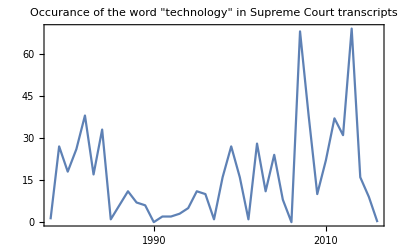

```mathematica
DateListPlot[Total/@GroupBy[wordCounts,First][[All,All,2]],PlotTheme->"Detailed",PlotLabel->"Occurance of the word \"technology\" in Supreme Court transcripts"]
```

#### Function

```mathematica
wordFrequency[docketAndText_,yearDict_,searchWordList_]:=Module[
{wordCounts,yearAbbreviation,year},
wordCounts=Map[
Function[
{entry},
yearAbbreviation=First@StringSplit[entry["Docket"],"-"];
year=If[
StringMatchQ[First@Characters@yearAbbreviation,"0"|"1"],
"20"<>yearAbbreviation,
"19"<>yearAbbreviation
]/.years;
{year,StringCount[entry["RawText"],searchWordList]}
],
docketAndText];

DateListPlot[Total/@GroupBy[wordCounts,First][[All,All,2]],PlotTheme->"Monochrome",PlotLabel->"Occurances of "<>ToString@searchWordList<>" in Supreme Court transcripts"]
]
```

```mathematica
years=AssociationMap[Interpreter["Date"],If[
StringMatchQ[First@Characters@#,"0"|"1"],
"20"<>#,
"19"<>#
]&/@Union[First@StringSplit[#,"-"]&/@sortedFullDataw[[All,"Docket"]]]];
```

```mathematica
docketAndText=sortedFullDataw[[All,{"Docket","RawText"}]];
```

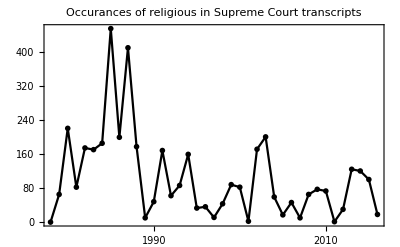

```mathematica
wordFrequency[docketAndText,years,"religious"]
```

#### Microsite

```mathematica
CloudPut[docketAndText,"junk/data"];
```

```mathematica
CloudGet["junk/data"];
```

```mathematica
With[
{yearDict=years},
CloudDeploy[
FormPage[
{"Terms"->"String"},
Function[
{formValues},
passThis=CloudGet["junk/data"];
terms=StringSplit[formValues["Terms"],","];
wordFrequency[passThis,yearDict,terms]
]],
"junk/test",
Permissions->"Public"
]
]
```

CloudObject[https://www.wolframcloud.com/objects/hannah.r.garringer/junk/test]

### Word Frequency Machine Learning

#### Word Frequency Prediction

```mathematica
features=Function[
{text},
{StringCount[text,"liberal"],StringCount[text,"constitution"]}
]/@sortedFullDataw[[All,"RawText"]];
```

```mathematica
outcomes=First/@sortedFullDataw[[All,"Decisions",All,3]];
```

```mathematica
fakeJudge=Classify[features->outcomes]
```

ClassifierFunction[…]

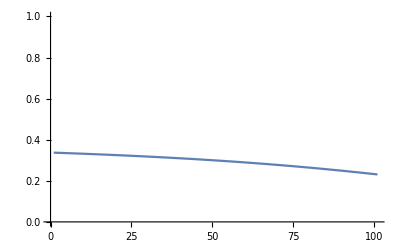

```mathematica
ListLinePlot[Table[fakeJudge[{0,x},"Probability"->2.],{x,0,100}],PlotRange->{0,1}]
```

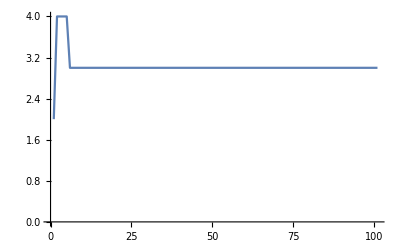

```mathematica
ListLinePlot@Table[fakeJudge[{x,0}],{x,0,100}]
```

```mathematica
(*TRY: Malign, Inaccurate, Basic rights, Alien*)
```

### Text Associations

#### Names to text

```mathematica
data=Association@Map[FileBaseName[#]->Import[#]&,samplew];
```

Import::infer: Cannot infer format of file .DS_Store.

```mathematica
exampleText=data[[1]];
```

```mathematica
StringSplit[exampleText,letter:Repeated[CharacterRange["A","Z"]]~~":":>letter<>":"];
```

```mathematica
splitAtProceedings=StringSplit[exampleText,"P R O C E E D I N G S"];
```

```mathematica
hasProceedings=Length@splitAtProceedings===2
```

True

```mathematica
transcripts=splitAtProceedings[[2]];
```

```mathematica
chars=Join[CharacterRange["A","Z"],{Whitespace,"."}]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,Whitespace,.}

```mathematica
names=StringTrim@StringCases[transcripts,name:Repeated[chars]~~":":>name];
ReverseSort@Counts@names
```

<|QUESTION→73,.
QUESTION→42,MR. GUTTENTAG→39,.
MR. KNEEDLER→26,MR. KNEEDLER→24,.
MR. GUTTENTAG→24,CHIEF JUSTICE REHNQUIST→2,.
REBUTTAL ARGUMENT OF LUCAS GUTTENTAG
ON BEHALF OF THE PETITIONERS
MR. GUTTENTAG→1,.
ORAL ARGUMENT OF EDWIN S. KNEEDLER
ON BEHALF OF THE RESPONDENT
MR. KNEEDLER→1,.
ORAL ARGUMENT OF LUCAS GUTTENTAG
ON BEHALF OF THE PETITIONER
MR. GUTTENTAG→1|>

#### Individual statements

```mathematica
transc=StringReplace[transcripts,".\n"->" "];
```

```mathematica
grouped=StringTrim/@Split[StringSplit[transc,name:Repeated[chars]~~":":>name],StringMatchQ[#,Repeated[chars]]&];
justwords=Delete[grouped,1];
```

```mathematica
groupedstat=GatherBy[justwords,First];
```

```mathematica
petitioner=StringDelete[DigitCharacter][Flatten@groupedstat[[2]]];
```

```mathematica
nonumbers1=StringDelete[DigitCharacter][Flatten@grouped];
```

#### Emotion measures

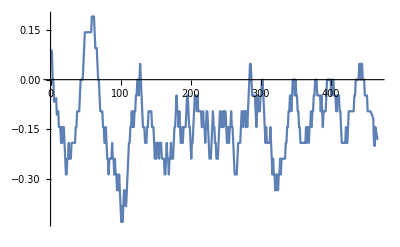

```mathematica
ListLinePlot[{MeanFilter[ReplaceAll[Classify["Sentiment",nonumbers1],{"Positive"->1,"Negative"->-1,Indeterminate->0,"Neutral"->0}],10]},PlotRange->All,Joined->True]
```

```mathematica
Mean@ReplaceAll[Classify["Sentiment",nonumbers1],{"Positive"->1,"Negative"->-1,Indeterminate->0,"Neutral"->0}]//N
```

-0.126338

```mathematica
plotemotion[emotion_String]:=ListLinePlot[{MeanFilter[ReplaceAll[Classify["Sentiment",emotion],{"Positive"->1,"Negative"->-1,Indeterminate->0,"Neutral"->0}],10]},PlotRange->All,Joined->True]
plotemotionmean[mean_String]:=Mean@ReplaceAll[Classify["Sentiment",mean]]
```

### Data Visualization

#### Liberal/Conservative

```mathematica
libcon=Flatten@Position[numericDataw[[1]],"docket"|"dateArgument"|"decisionDirection",{1}]
```

{14,16,42}

```mathematica
goodexcel2=Part[numericDataw,All,libcon]
```

{{docket,dateArgument,decisionDirection},{24,Wed 9 Jan 1946 00:00:00GMT-4.,2.},{24,Wed 9 Jan 1946 00:00:00GMT-4.,2.},{24,Wed 9 Jan 1946 00:00:00GMT-4.,2.},91756,{16-992,,2.},{16-992,,2.},{16-992,,2.},{16-992,,2.}}
 |  |  |  |

```mathematica
matchedcases2=Select[goodexcel2,MemberQ[caseNumbersFromTranscriptsw,#[[1]]]&];
```

```mathematica
singlematchedcases2=Union@matchedcases2;
```

```mathematica
datedecision2=Transpose@Delete[Transpose@singlematchedcases2,List/@{1}];
```

```mathematica
findatedecision2=Drop[Sort[datedecision2],1;;16];
```

```mathematica
dataplot2=SplitBy[SortBy[findatedecision2,Last],Last];
```

```mathematica
liberal=;
con=;
```

#### Liberal/Con Plot

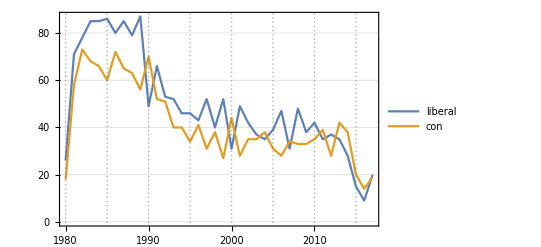

```mathematica
DateListPlot[{liberal,con},PlotTheme->"Detailed",FrameTicks->{DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]],Automatic},PlotLegends->{"liberal","con"}]
```

#### Total vote direction

```mathematica
excelheaders=Flatten@Position[numericDataw[[1]],"docket"|"dateArgument"|"caseDisposition",{1}];
```

```mathematica
goodexcel=Part[numericDataw,All,excelheaders];
```

```mathematica
matchedcases=Select[goodexcel,MemberQ[caseNumbersFromTranscriptsw,#[[1]]]&];
```

```mathematica
singlematchedcases=Union@matchedcases;
```

```mathematica
datedecision=Transpose@Delete[Transpose@singlematchedcases,List/@{1}];
```

```mathematica
findatedecision=Drop[Sort[datedecision],1;;16];
```

```mathematica
assoc=#1->#2&@@@findatedecision;
```

```mathematica
finaldatedecision=SplitBy[SortBy[assoc,Last],Last];
```

```mathematica
two=Extract[finaldatedecision,1];
three=Extract[finaldatedecision,2];
four=Extract[finaldatedecision,3];
five=Extract[finaldatedecision,4];
six=Extract[finaldatedecision,5];
seven=Extract[finaldatedecision,6];
eight=Extract[finaldatedecision,7];
nine=Extract[finaldatedecision,8];
ten=Extract[finaldatedecision,9];
```

#### Vote Histogram Over Time

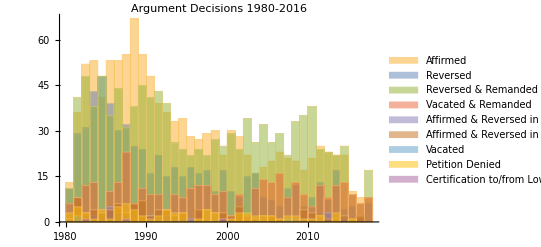

```mathematica
DateHistogram[{two,three,four,five,six,seven,eight,nine,ten},"Year",DateTicksFormat->{"","","Year"},ChartLegends->{"Affirmed","Reversed","Reversed & Remanded","Vacated & Remanded","Affirmed & Reversed in Part","Affirmed & Reversed in Part & Remanded","Vacated","Petition Denied","Certification to/from Lower Court"},Ticks->{DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]],Automatic},ChartLabels->Placed[{"Argument Decisions 1980-2016"},Above]]
```

#### Line Plot Over Time

```mathematica
dataplot=SplitBy[SortBy[findatedecision,Last],Last];
```

```mathematica
twoP=;
threeP=;
fourP=;
fiveP=;
sixP=;
sevenP=;
eightP=;
nineP=;
tenP=;
```

#### Date List Plot Over Time

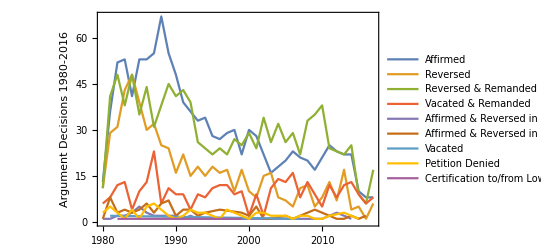

```mathematica
DateListPlot[{twoP,threeP,fourP,fiveP,sixP,sevenP,eightP,nineP,tenP},"Year",DateTicksFormat->{" ", " ", "Year"},PlotLegends->{"Affirmed","Reversed","Reversed & Remanded","Vacated & Remanded","Affirmed & Reversed in Part","Affirmed & Reversed in Part & Remanded","Vacated","Petition Denied","Certification to/from Lower Court"},FrameLabel->"Argument Decisions 1980-2016",FrameTicks->{DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]],Automatic}]
```

#### Total Vote Distribution

```mathematica
finaldecision=Flatten@findatedecision[[All,2]];
```

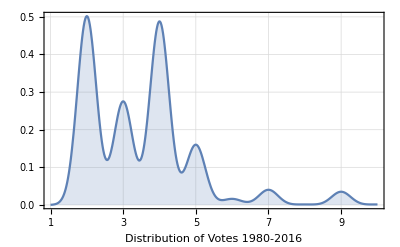

```mathematica
Plot[PDF[SmoothKernelDistribution[finaldecision],x],{x,1,10},FrameTicks->{Range@10,Automatic},Filling->Axis,FrameLabel->"Distribution of Votes 1980-2016",PlotTheme->"Detailed",PlotLegends->None]
```

### Steps left to do:

• Fix spelling errors [Interpreter]
• Machine learning on each justice' s questions and answers // 2000-2016
	• Separate into sections and run each 
• Machine learning on number of words asked //1978-2000
• Machine learning on whether high emotion questions result in negative or positive
• Statistics on whether justices are liberal or conservative and how that affects outcome
• More detailed analysis on chief justice’s orientation and impact on direction of vote
• Start looking at which justices are interrupted when
• Active v. Passive verbs
• Look for cases that resulted in the law getting changed // Remanded, coded as 3, 4, 5, 7